# The simulation when the cylinder rolls around on the ground

## Define equations

```mathematica
eq={
m(x0''[t]+R(θ''[t]Cos[θ[t]]-θ'[t]^2 Sin[θ[t]]))==-f2[t] Cos[θ[t]]+Fn2[t] Sin[θ[t]],
m R(-θ''[t] Sin[θ[t]]-θ'[t]^2 Cos[θ[t]])==f2[t] Sin[θ[t]]+Fn2[t] Cos[θ[t]]-m g,
f2[t]-f1[t]==x0''[t]/R^2 i,
f1[t]+f2[t] Cos[θ[t]]+Fn2[t] Sin[θ[t]]==m x0''[t]
}
```

{m (x0''[t]+R (-Sin[θ[t]] θ'[t]^2+Cos[θ[t]] θ''[t]))==-Cos[θ[t]] f2[t]+Fn2[t] Sin[θ[t]],m R (-Cos[θ[t]] θ'[t]^2-Sin[θ[t]] θ''[t])==-g m+Cos[θ[t]] Fn2[t]+f2[t] Sin[θ[t]],-f1[t]+f2[t]==(i x0''[t])/R^2,f1[t]+Cos[θ[t]] f2[t]+Fn2[t] Sin[θ[t]]==m x0''[t]}

## Define initial conditions

```mathematica
initial={x0[0]==0,x0'[0]==0,θ[0]==1,θ'[0]==0}
```

{x0[0]==0,x0'[0]==0,θ[0]==1,θ'[0]==0}

## Define parameters

```mathematica
params={m->1,g->1,i->1,R->1}
```

{m→1,g→1,i→1,R→1}

## Control equation

```mathematica
ceq=f2[t]==0
```

f2[t]==0

## Solve ODE

```mathematica
sol=NDSolveValue[{eq,initial,ceq}/.params,{x0,θ},{t,0,20}]
```

{InterpolatingFunction[{{0., 20.}}, <>],InterpolatingFunction[{{0., 20.}}, <>]}

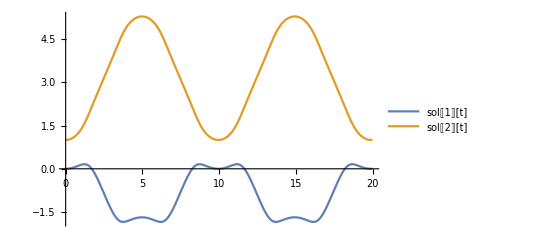

```mathematica
Plot[{sol[[1]][t],sol[[2]][t]},{t,0,20},PlotRange->All,PlotLegends->"Expressions"]
```